# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - 1404 / 4 / 9)

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Patched 2 FeynArts models.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

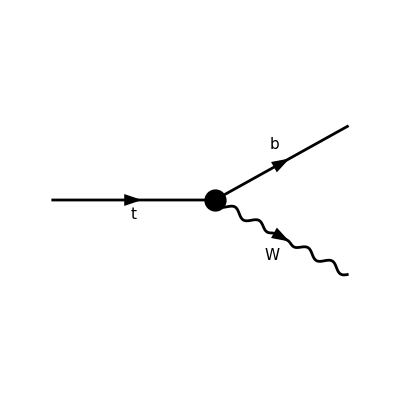

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

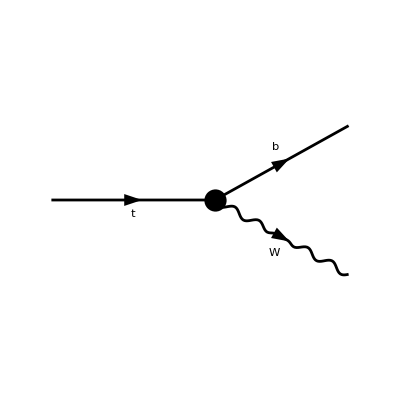

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc139L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc139R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc139L =(FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
     gc139R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 Lambda^4 sw)ⅈ δ_Col1Col2 (-4 sw vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 sw vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(e Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2 sw)+(e (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2 sw)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8 sw^2)Nc (4 e^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 e Lambda^2 Conjugate[CHud] (e Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt sw (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+√2 mb sw (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3] (2 ⅈ (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))-(OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))-(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+e mb mt Conjugate[CKM3x3] ((ε̄)^*(pW)·ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 mb Conjugate[CKM3x3] (2 e Conjugate[CudH4D] (√2 sw vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 ⅈ (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))-(OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))-(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)))+e mt ((ε̄)^*(pW)·ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^3-2 sw Conjugate[C1qdWH3] (8 mt sw vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))+2 ⅈ √2 e (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))+√2 e (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))+√2 e ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 sw Conjugate[CbW] (-8 mt sw vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 e (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 e (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 e ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 (e^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 e mt sw (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 sw^2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))) vev^2)+(Conjugate[CKM3x3])^2 (-16 e^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 e^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW e mt sw vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 sw^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 sw^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 sw^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 sw^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 sw^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 e^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ e^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 e mt sw vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW e mt sw vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 sw^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 sw^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 e^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW sw^2 vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW sw^2 vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW sw^2 vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW sw^2 vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW sw^2 vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D e^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 e^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW e mt sw vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 e mt sw vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW sw^2 vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW sw^2 vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 e^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW e mt sw vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW e mt sw vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 sw^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 sw^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 sw^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 sw^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 sw^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 e^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 e^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 e^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-e^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 e mt sw vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 sw^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 sw^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D e^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ e^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 e mt sw vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 e^2 (Conjugate[C2q2H4D])^2 vev^8+8 e^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(e^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D e^2 Conjugate[C3q2H4D] vev^6+16 e^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 e^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ e^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 e^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 sw^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+e^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ sw vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 sw vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 e mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D e^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 e^2 (Conjugate[C2q2H4D])^2 vev^8+8 e^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(e^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D e^2 Conjugate[C3q2H4D] vev^6+16 e^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 e^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ e^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 e^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 sw^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+e^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 sw vev (OverBar[pW]·(ε̄)^*(pW)) (4 sw vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 e mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 e^2 (Conjugate[C2q2H4D])^2 vev^8+8 e^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(e^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D e^2 Conjugate[C3q2H4D] vev^6+16 e^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 e^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ e^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 e^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 sw^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+e^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 sw vev (OverBar[pW]·ε̄(pW)) (4 sw vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 e mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
(* Sum over all polarization of W boson for calculate total decay width*)
```

```mathematica
SP[p2,p2]=m2^2;
```

```mathematica
pr1=PolarizationVector[p2,μ]ComplexConjugate[PolarizationVector[p2,ν]]
```

(ε̄)^μ(p2) ((ε̄)^*)^ν(p2)

```mathematica
DoPolarizationSums[pr1,p2]
```

(OverBar[p2]^μ OverBar[p2]^ν)/m2^2-(ḡ)^μν

```mathematica
DoPolarizationSums[lsAsqq,pW]/.sw->e/g//FullSimplify
```

1/(32 Lambda^8 OverBar[pW]^2)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pt]) OverBar[pW]^2) vev^4-8 g Lambda^2 Conjugate[CHud] (3 OverBar[pW]^2 (mb Conjugate[CKM3x3] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))-2 √2 mt vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (OverBar[pb]·OverBar[pW]))-g vev^4 Conjugate[CudH4D] (2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pt]) OverBar[pW]^2)) vev^2-24 mb Conjugate[CKM3x3] OverBar[pW]^2 (g Conjugate[CudH4D] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) OverBar[pW]^2+√2 g (OverBar[pt]·OverBar[pW]) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 (g^2 (Conjugate[CudH4D])^2 (2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pt]) OverBar[pW]^2) vev^8+12 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (OverBar[pb]·OverBar[pW]) OverBar[pW]^2 vev^5-8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 OverBar[pW]^2 ((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])))+(Conjugate[CKM3x3])^2 ((OverBar[pb]·OverBar[pt]) OverBar[pW]^2 (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+2 (OverBar[pb]·OverBar[pW]) ((OverBar[pt]·OverBar[pW]) (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 ⅈ Im(C3q2H4D) Re(C2q2H4D))) g^2+24 √2 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) OverBar[pW]^2 (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) g+64 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2 (OverBar[pt]·OverBar[pW]) OverBar[pW]^2)))

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={Ew,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
Msqt1=(1/(32 Lambda^8 MinkSP[Pw,Pw])) Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^4-8 g Lambda^2 Conjugate[CHud] (3 MinkSP[Pw,Pw] (mb Conjugate[CKM3x3] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 Sqrt[2] mt vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) MinkSP[Pb,Pw])-g vev^4 Conjugate[CudH4D] (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw])) vev^2-24 mb Conjugate[CKM3x3] MinkSP[Pw,Pw] (g Conjugate[CudH4D] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw]+Sqrt[2] g MinkSP[Pt,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))) vev+4 (g^2 (Conjugate[CudH4D])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^8+12 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] MinkSP[Pb,Pw] MinkSP[Pw,Pw] vev^5-8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 MinkSP[Pw,Pw] (MinkSP[Pb,Pt] MinkSP[Pw,Pw]-4 MinkSP[Pb,Pw] MinkSP[Pt,Pw]))+(Conjugate[CKM3x3])^2 (MinkSP[Pb,Pt] MinkSP[Pw,Pw] (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+2 MinkSP[Pb,Pw] (MinkSP[Pt,Pw] (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 I Im[C3q2H4D] Re[C2q2H4D])) g^2+24 Sqrt[2] mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) g+64 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2 MinkSP[Pt,Pw] MinkSP[Pw,Pw])))//FullSimplify
```

1/(32 Lambda^8 (Ew-pb) (Ew+pb))Nc (4 g^2 Lambda^4 mt (3 Eb Ew^2-(Eb-2 Ew) pb^2) (Conjugate[CHud])^2 vev^4-8 g Lambda^2 Conjugate[CHud] (g mt (Eb (pb^2-3 Ew^2)-2 Ew pb^2) Conjugate[CudH4D] vev^4+3 (Ew-pb) (Ew+pb) (mb mt Conjugate[CKM3x3] (2 g Lambda^2 Conjugate[C3phiq] vev^2+2 √2 Ew (2 CtW Lambda^2+C1quWH3 vev^2) vev+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))-2 √2 mt (pb^2+Eb Ew) vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]))) vev^2-24 mb (Ew-pb) (Ew+pb) Conjugate[CKM3x3] (g mt Conjugate[CudH4D] (2 g Lambda^2 Conjugate[C3phiq] vev^2+2 √2 Ew (2 CtW Lambda^2+C1quWH3 vev^2) vev+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt (Ew-pb) (Ew+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 Ew g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 mt (g^2 (3 Eb Ew^2-(Eb-2 Ew) pb^2) (Conjugate[CudH4D])^2 vev^8+12 √2 g (Ew-pb) (Ew+pb) (pb^2+Eb Ew) (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] vev^5+8 (Ew-pb) (Ew+pb) (3 Eb Ew^2+(Eb+4 Ew) pb^2) (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2)+(Conjugate[CKM3x3])^2 (2 mt (pb^2+Eb Ew) (Ew (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 ⅈ Im(C3q2H4D) Re(C2q2H4D))) g^2+24 √2 (Ew-pb) (Ew+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) g+64 Ew (Ew-pb) (Ew+pb) (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2)+Eb mt (Ew-pb) (Ew+pb) ((16 Lambda^8+16 (C2q2H4D+C3q2H4D) vev^4 Lambda^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8) g^2+vev^2 (4 (Conjugate[C2q2H4D])^2 vev^6+(Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 ⅈ Im(C3q2H4D) Re(C2q2H4D) vev^6+16 Lambda^4 (Conjugate[C3phiq])^2 vev^2+8 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D] vev^2-16 Lambda^4 Re(C3q2H4D) vev^2+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) g^2-32 (Ew-pb) (Ew+pb) (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2)))

```mathematica
Ew=(mt^2+mw^2-mb^2)/(2 mt);
Eb=mt-Ew;
(*pw=pb;*)
(*pb=(1/(2 mt)) Sqrt[mt^2 - (mb + mw)^2] Sqrt[mt^2 - (mb - mw)^2];*)
```

```mathematica
(*Compute decay width systematically*)
```

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthtotal=Integrate[Msqt1*dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar}//FullSimplify
```

1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^4 (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) vev^4 (Conjugate[CHud])^2 mt^4+16 vev^2 (g^2 (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) (Conjugate[CudH4D])^2 vev^6-8 mw^2 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) (Conjugate[C1qdWH3])^2 vev^4-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) Conjugate[CbW] Conjugate[CudH4D] vev^3-4 mw^2 Conjugate[C1qdWH3] (3 √2 g mt (mb^2-mt^2+mw^2) Conjugate[CudH4D] vev^3+8 Lambda^2 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) Conjugate[CbW]) vev^2-32 Lambda^4 mw^2 (mw^4+(mb^2+mt^2) mw^2-2 (mb^2-mt^2)^2) (Conjugate[CbW])^2) mt^4-32 g Lambda^2 vev^2 Conjugate[CHud] (-g (-2 mw^4+(mb^2+mt^2) mw^2+(mb^2-mt^2)^2) Conjugate[CudH4D] vev^4+6 √2 mt mw^2 (mb^2-mt^2+mw^2) Conjugate[C1qdWH3] vev^3+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) Conjugate[CbW] vev+6 mb mw^2 Conjugate[CKM3x3] (g mt (2 Conjugate[C3phiq] Lambda^2+vev^2 (Conjugate[C2q2H4D]-Re(C3q2H4D))) vev^2-√2 (mb^2-mt^2-mw^2) (C1quWH3 vev^3+2 CtW Lambda^2 vev)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4))) mt^4+48 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (-2 g Lambda^2 mt Conjugate[C3phiq] vev^2+√2 (mb^2-mt^2-mw^2) (2 CtW Lambda^2+C1quWH3 vev^2) vev-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))-mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) mt+(Conjugate[CKM3x3])^2 (4 mt^4 (mb^2-mt^2+mw^2) ((mb^2-mt^2-mw^2) (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 ⅈ Im(C3q2H4D) Re(C2q2H4D))) g^2-48 √2 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) g-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2)-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-((16 Lambda^8+16 (C2q2H4D+C3q2H4D) vev^4 Lambda^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8) g^2)-vev^2 (4 (Conjugate[C2q2H4D])^2 vev^6+(Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 ⅈ Im(C3q2H4D) Re(C2q2H4D) vev^6+16 Lambda^4 (Conjugate[C3phiq])^2 vev^2+8 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D] vev^2-16 Lambda^4 Re(C3q2H4D) vev^2+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) g^2+32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2)))

```mathematica
(*SM Limit is correct*)
```

```mathematica
DecayWidthtotalSM=DecayWidthtotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 Nc (Conjugate[CKM3x3])^2 √(-((mb-mt-mw) (mb+mt-mw))) (mw^2 (mb^2+mt^2)+(mb^2-mt^2)^2-2 mw^4) √(mt^2-(mb+mw)^2))/(64 π mt^3 mw^2)

```mathematica
Limit[DecayWidthtotalSM,mb->0]//FullSimplify
```

(g^2 Nc (Conjugate[CKM3x3])^2 (mt^6-3 mt^2 mw^4+2 mw^6))/(64 π mt^3 mw^2)

```mathematica
(*Define parameters and constants*)
Lambda=1000; sw=0.4834;e=0.31345;vev=246.2205;g=0.6483;mb=4.7;mt= 172; mw=79.8;CKM3x3=1;
FCGV["EL"]=e;
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
DecayWidthtotal
```

6.3523×10^-44 Nc (7.1997×10^15 (-3.78283×10^23 Conjugate[CudH4D]-4.74368×10^25)-1.41336×10^22 (-2.33825×10^18 Conjugate[CudH4D]-1.78922×10^20)+8.4895×10^14 (9.18998×10^22 (Conjugate[CudH4D])^2+1.72724×10^25 Conjugate[CudH4D]+1.3261×10^27)+(2.72653×10^43+0. ⅈ))

```mathematica
CudH4D=0.5;
```

```mathematica
DecayWidthtotal
```

(1.94386+0. ⅈ) Nc

```mathematica
DecayWidthtotalSM
```

1.46756 Nc